## Conventional poverty trap: S-shape vs L-shape

In this file, several variables of the conventional Solow growth poverty trap model are varied.

```mathematica
A=10;
α1=0.4;
s1=0.1;
s2=0.2;
s3=10;
d=2;
δP=Rationalize[0.5];
n=Rationalize[0.5];
```

```mathematica
f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
```

```mathematica
Savings:=sf[kP] f[kP]
Depreciation:=(δP+n) kP
```

Changing parameter A

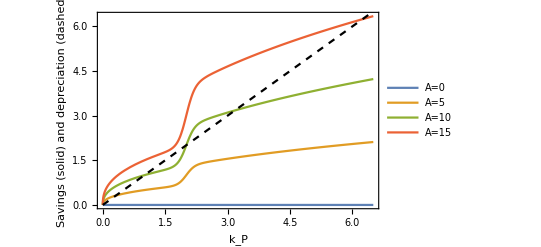

```mathematica
ValuesA={0,5, 10,15};
p1=Plot[Evaluate[Table[Savings, {A, ValuesA}]], {kP,0,6.5},
Frame->True, FrameLabel->{"k_P", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"A=",x}],{x,ValuesA}],{Left,Top}]];
p2=Plot[Depreciation,{kP,0,6.5},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

A: exogenous level of technology
Higher A increases savings
No influence on S-shape, except when A=0

### Changing parameter α1

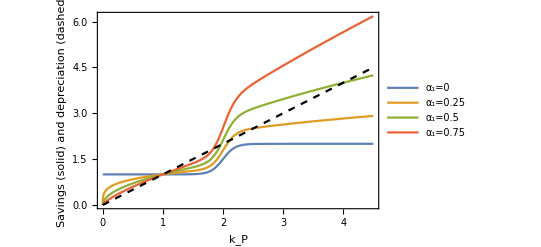

```mathematica
Valuesα1={0, 0.25,0.5,0.75};
p1=Plot[Evaluate[Table[Savings, {α1, Valuesα1}]], {kP,0,4.5},
Frame->True, FrameLabel->{"k_P", "Savings (solid) and 
depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"α_1=",x}],{x,Valuesα1}],{Left, Top}]];
p2=Plot[Depreciation,{kP,0,4.5},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

α1: output elasticity of capital
No influence on S-shape

### Changing parameter s1

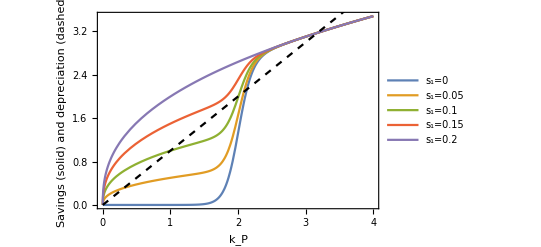

```mathematica
Valuess1={0,0.05,0.1,0.15,0.2};
p1=Plot[Evaluate[Table[Savings, {s1, Valuess1}]], {kP,0,4},
Frame->True, FrameLabel->{"k_P", "Savings (solid) and 
depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s_1=",x}],{x,Valuess1}],{Right,Bottom}]];
p2=Plot[Depreciation,{kP,0,4},PlotStyle->{Black, Dashed}];
Show[{p1,p2}]
```

s1: initial saving rate before threshold d
S-shape if s1 < s2
L-shape if s1 = s2

### Changing parameter s2

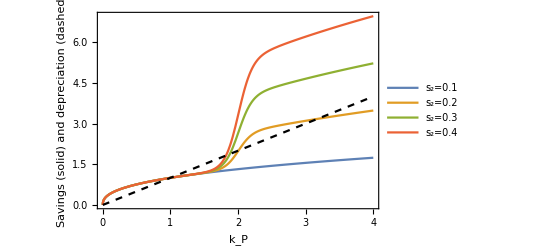

```mathematica
Valuess2={0.1,0.2,0.3,0.4};
p1=Plot[Evaluate[Table[Savings, {s2, Valuess2}]], {kP,0,4},
Frame->True, FrameLabel->{"k_P", "Savings (solid) and 
depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s_2=",x}],{x,Valuess2}],{Left,Top}]];
p2=Plot[Depreciation,{kP,0,4},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

s2: savings rate after threshold d
S-shape if s2 > s1
L-shape if s2 = s1

### Changing parameter s3

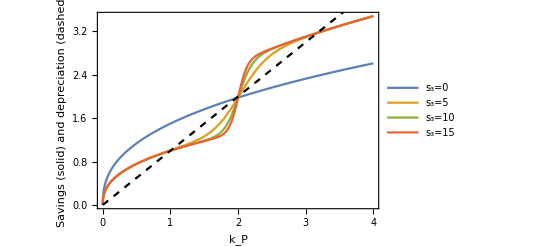

```mathematica
Valuess3={0,5, 10,15}; 
p1=Plot[Evaluate[Table[Savings, {s3, Valuess3}]], {kP,0,4},
Frame->True, FrameLabel->{"k_P", "Savings (solid) and 
depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s_3=",x}],{x,Valuess3}],{Right,Bottom}]];
p2=Plot[Depreciation,{kP,0,4},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

S-shape if s3 > 0
L-shape if s3 <= 0

### Changing parameter d

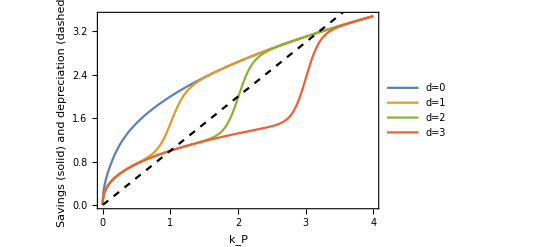

```mathematica
Valuesd={0,1,2,3};
p1=Plot[Evaluate[Table[Savings, {d, Valuesd}]], {kP,0,4},
Frame->True, FrameLabel->{"k_P", "Savings (solid) and 
depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"d=",x}],{x,Valuesd}],{Right,Bottom}]];
p2=Plot[Depreciation,{kP,0,4},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]
```

d is where the S-shape occurs